```mathematica
ClearAll["Global'*"]
G[r1_,r2_]:=3/40{{r1^2/((r1^2+r2^2)^(3/2))+1/((r1^2+r2^2)^(1/2)),r1 r2/((r1^2+r2^2)^(3/2))},{r1 r2/((r1^2+r2^2)^(3/2)),r2^2/((r1^2+r2^2)^(3/2))+1/((r1^2+r2^2)^(1/2))}};
G2[{r1_,r2_}]:=3/40{{r1^2/((r1^2+r2^2)^(3/2))+1/((r1^2+r2^2)^(1/2)),r1 r2/((r1^2+r2^2)^(3/2))},{r1 r2/((r1^2+r2^2)^(3/2)),r2^2/((r1^2+r2^2)^(3/2))+1/((r1^2+r2^2)^(1/2))}};
G3[{r1_,r2_}]:=3/40{{r1^2/((r1^2+r2^2)^(3/2))+1/((r1^2+r2^2)^(1/2)),r1 r2/((r1^2+r2^2)^(3/2))},{r1 r2/((r1^2+r2^2)^(3/2)),r2^2/((r1^2+r2^2)^(3/2))+1/((r1^2+r2^2)^(1/2))}};
GG[x_,e_]:= 3/40 (e+Dot[x,e]x/Norm[x]^2)/Norm[x];
GD[x_,q_,e_]:= 3/40((Dot[x,q]e-Dot[e,x]q-Dot[q,e]x)/Norm[x]+(3Dot[e,x]Dot[q,x]x)/Norm[x]^3)/Norm[x]^2;
D[x_,e_]:=3/40(-e+3Dot[e,x]x/Norm[x]^2)/Norm[x]^3;
```

SetDelayed::write: Tag D in ∂_e_ x_ is Protected.

```mathematica
g1[r1_,r2_]={r1^2/((r1^2+r2^2)^(3/2))+1/((r1^2+r2^2)^(1/2)),r1 r2/((r1^2+r2^2)^(3/2))};
g2[r1_,r2_]={r1 r2/((r1^2+r2^2)^(3/2)),r2^2/((r1^2+r2^2)^(3/2))+1/((r1^2+r2^2)^(1/2))};
```

```mathematica
y0:={100,100}
```

```mathematica
y0hat:=y0/Norm[y0];
theta:=0;
```

```mathematica
epsilon:=1/Norm[y0];
```

```mathematica
x1[t_]:={2,0}+RotationMatrix[theta].{Piecewise[{{ Mod[t,1],0 ≤ Mod[t,1] ≤ 1/4},{1/4,1/4 ≤ Mod[t,1] ≤ 1/2},{1/4-( Mod[t,1]-1/2),1/2≤ Mod[t,1]≤ 3/4},{0,3/4 ≤ Mod[t,1]≤ 1}}],0};
x2[t_]:={Piecewise[{{0,0 ≤ Mod[t,1] ≤ 1/4},{-( Mod[t,1]-1/4),1/4 ≤ Mod[t,1] ≤ 1/2},{-1/4,1/2≤ Mod[t,1]≤ 3/4},{-1/4 + ( Mod[t,1]-3/4),3/4 ≤ Mod[t,1]≤ 1}}],0};
```

```mathematica
dx1[t_]:=RotationMatrix[theta].{Piecewise[{{1,0 ≤ Mod[t,1] ≤ 1/4},{0,1/4 ≤ Mod[t,1] ≤ 1/2},{-1,1/2≤ Mod[t,1]≤ 3/4},{0,3/4 ≤ Mod[t,1]≤ 1}}],0};
dx2[t_]:={Piecewise[{{0,0 ≤ Mod[t,1] ≤ 1/4},{-1,1/4 ≤ Mod[t,1] ≤ 1/2},{0,1/2≤ Mod[t,1]≤ 3/4},{1,3/4 ≤ Mod[t,1]≤ 1}}],0};
```

```mathematica
x11[t_?NumericQ]:=x1[t];
x21[t_?NumericQ]:=x2[t];
dx11[t_?NumericQ]:=dx1[t];
dx21[t_?NumericQ]:=dx2[t];
```

```mathematica
a=0.1;
mu=1;
```

```mathematica
Ginv[{r1_,r2_},a_]={{(2 (r1^2+2 r2^2))/(3 a √(r1^2+r2^2)),-((2 r1 r2)/(3 a √(r1^2+r2^2)))},{-((2 r1 r2)/(3 a √(r1^2+r2^2))),(2 (2 r1^2+r2^2))/(3 a √(r1^2+r2^2))}};

K[{r1_,r2_},a_]={{(9 a^2 (-9 a^2+8 r1^2+2 r2^2))/(4 (-8 (r1^2+r2^2)^2+9 a^2 (5 r1^2+6 r1 r2+5 r2^2))),(81 a^4+54 a^2 r1 r2)/(4 (-8 (r1^2+r2^2)^2+9 a^2 (5 r1^2+6 r1 r2+5 r2^2)))},{(81 a^4+54 a^2 r1 r2)/(4 (-8 (r1^2+r2^2)^2+9 a^2 (5 r1^2+6 r1 r2+5 r2^2))),(9 a^2 (-9 a^2+2 r1^2+8 r2^2))/(4 (-8 (r1^2+r2^2)^2+9 a^2 (5 r1^2+6 r1 r2+5 r2^2)))}};
```

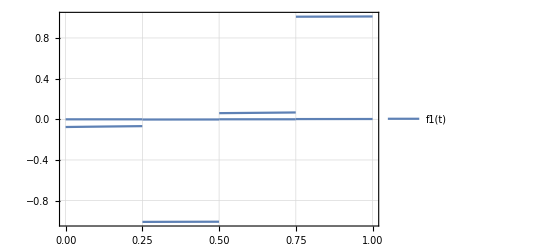

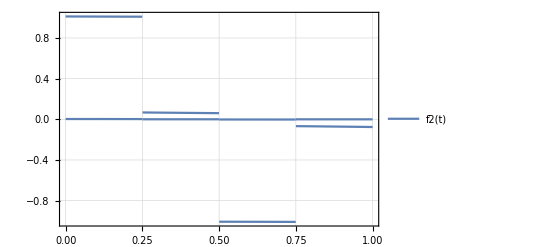

```mathematica
f1[t_]=K[x1[t]-x2[t],a].(Ginv[x1[t]-x2[t],a].dx1[t]-(Ginv[x1[t]-x2[t],a].Ginv[x1[t]-x2[t],a]).dx2[t]);
f2[t_]=K[x1[t]-x2[t],a].(Ginv[x1[t]-x2[t],a].dx2[t]-(Ginv[x1[t]-x2[t],a].Ginv[x1[t]-x2[t],a]).dx1[t]);
Print[Plot[f1[t],{t,0,1},PlotTheme->"Detailed",PlotRange->All]];
Print[Plot[f2[t],{t,0,1},PlotTheme->"Detailed",PlotRange->All]];
```

```mathematica
diffforces = ParametricNDSolveValue[{c'[t] == G2[c[t] - x11[t]].f1[t] + G2[c[t] - x21[t]].f2[t], c[0] == {b1,b2}}, c[1]-c[0],{t, 0, 1}, {b1,b2}, Method -> "StiffnessSwitching"];
intf=NIntegrate[{f1[t]+f2[t]},{t,0,1}][[1]];
diffforcesapprox[p_?NumericQ,q_?NumericQ] =(G2[{p,q}/((p^2+q^2)^(1/2))]/((p^2+q^2)^(1/2))).intf;
```

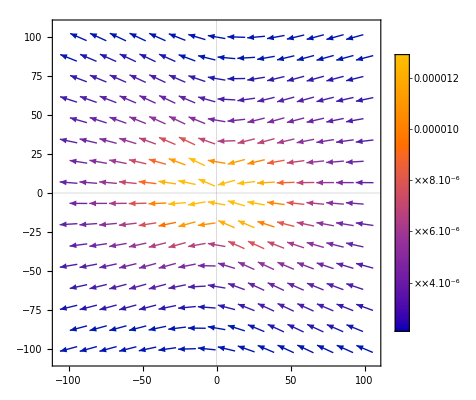

```mathematica
plot=VectorPlot[diffforcesapprox[p,q],{p,-100,100},{q,-100,100},PlotTheme->"Scientific",PlotLegends->Automatic,ColorFunction->"TemperatureMap"];
Print[plot];
```